```mathematica
geom1={{0.5,1.0,c},{-0.5,1.0,c},{-0.5,-1.0,c},{0.5,-1.0,c},{0.5,1.0,c}}[[All,1;;2]];
```

```mathematica
geom2=Table[RotationMatrix[Pi/5].geom1[[i]],{i,1,Length[geom1]}];
```

```mathematica
geom3=Table[RotationMatrix[-Pi/5].geom1[[i]],{i,1,Length[geom1]}];
```

```mathematica
arcgen[{p1_,p2_,p3_},r_,n_]:=Module[{dc=Normalize[p1-p2]+Normalize[p3-p2],cc,th,ie,det},
If[EuclideanDistance[dc,Projection[dc,p1-p2]]<10^-3,ie=0,ie=1/EuclideanDistance[dc,Projection[dc,p1-p2]]];
cc=p2+r dc*ie;
If[ie==0,det=0,det=Det[PadRight[{p1,p2,p3},{3,3},1]]];
th=Sign[det] (π-VectorAngle[p3-p2,p1-p2])/(n-1);(*при обходе против часовой стрелке sign = 1*)
NestList[RotationTransform[th,cc],p2+Projection[cc-p2,p1-p2],n-1]]
roundedPolygon[Polygon[opts_?MatrixQ],r_?NumericQ,n:(_Integer?Positive):12]:=With[{pts=Split[opts][[All,1]]},Polygon[Flatten[arcgen[#,r,n]&/@Partition[If[TrueQ[First[pts]==Last[pts]],Most,Identity][pts],3,1,{2,-2}],1]]];
```

```mathematica
pts=geom2[[1;;-1]];
pol=Polygon[pts];
ListAnimate[Table[Graphics[{EdgeForm[Thick],White,roundedPolygon[pol,r]}],{r,.01,0.3,.01}]]
```

```mathematica
pp=roundedPolygon[pol,0.03][[1]];
ppall=pp~Join~{pp[[1]]}
ListLinePlot[ppall,AspectRatio->Automatic,Mesh->All,MeshStyle->Directive[Red,PointSize->0.001]]
```

```mathematica
Norm[{-0.16564319753622522,1.0786391106899358}-{-0.16839975322470468,1.0819136801808205}]
```

0.00428035

```mathematica
6/0.004280350991953952
```

1401.75

```mathematica
SplitLine[a_List,b_List,h_,OptionsPattern[{FirstPoint->True,LastPoint->True}]]:=Module[{dr,np,i,j},np=Ceiling[Norm[b-a]/h];dr=(b-a)/np;(*Print[np];Print[dr];*)
i=If[OptionValue[FirstPoint],0,1];
j=If[OptionValue[LastPoint],np,np-1];
Table[a+q dr,{q,i,j}]]
```

```mathematica
ppall
```

{{-0.165643,1.07864},{-0.1684,1.08191},{-0.171594,1.08476},{-0.175162,1.08713},{-0.179029,1.08896},{-0.183119,1.09023},{-0.187346,1.0909},{-0.191626,1.09096},{-0.195871,1.09041},{-0.199995,1.08926},{-0.203914,1.08754},{-0.207547,1.08528},{-0.968023,0.532758},{-0.971298,0.530001},{-0.974147,0.526807},{-0.976512,0.523239},{-0.978346,0.519372},{-0.97961,0.515282},{-0.98028,0.511055},{-0.980341,0.506775},{-0.979792,0.50253},{-0.978645,0.498406},{-0.976923,0.494487},{-0.97466,0.490854},{0.165643,-1.07864},{0.1684,-1.08191},{0.171594,-1.08476},{0.175162,-1.08713},{0.179029,-1.08896},{0.183119,-1.09023},{0.187346,-1.0909},{0.191626,-1.09096},{0.195871,-1.09041},{0.199995,-1.08926},{0.203914,-1.08754},{0.207547,-1.08528},{0.968023,-0.532758},{0.971298,-0.530001},{0.974147,-0.526807},{0.976512,-0.523239},{0.978346,-0.519372},{0.97961,-0.515282},{0.98028,-0.511055},{0.980341,-0.506775},{0.979792,-0.50253},{0.978645,-0.498406},{0.976923,-0.494487},{0.97466,-0.490854},{-0.165643,1.07864}}

```mathematica
vertex=Flatten[Table[SplitLine[ppall[[i]],ppall[[i+1]],0.2,LastPoint->False],{i,Length@ppall-1}],1];
```

```mathematica
n=Length@vertex
```

74

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["house3",
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.14   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2026/03/06     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2026 I. Marchevsky, K. Sokol, E. Ryatina, A. Kolganova   |
*-----------------------------------------------------------------------------*
| File name: house3         "<>StringRepeat[" ",50]<>"|
| Info: house3 ("<>TextString[n]<>" panels)"<>StringRepeat[" ",54-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/ 
"}~Join~{"r = {"}
~Join~
Table[{"{",TextString@vertex[[i,1]],",",TextString@vertex[[i,2]],"},"},{i,n-1}]
~Join~
{{"{",TextString@vertex[[-1,1]],",",TextString@vertex[[-1,2]],"}"}}
~Join~
{{"};"}}
,"Table"]
```

house3

```mathematica
(*****************Визуализация*********************)
```

```mathematica
house1={{0.5,0.97},{0.49969464325642793,0.9742694451481986},{0.4987847892084349,0.9784519767052429},{0.49728895986063554,0.9824624503900568},{0.4952376059849354,0.9862192245236683},{0.4926724872306277,0.989645822018359},{0.48964582201835843,0.9926724872306283},{0.4862192245236677,0.9952376059849359},{0.48246245039005636,0.997288959860636},{0.4784519767052426,0.9987847892084354},{0.4742694451481982,0.9996946432564284},{0.4699999999999996,1.0000000000000004},{-0.47,1.},{-0.47426944514819847,0.999694643256428},{-0.47845197670524275,0.9987847892084349},{-0.4824624503900564,0.9972889598606356},{-0.4862192245236677,0.9952376059849355},{-0.4896458220183584,0.9926724872306278},{-0.4926724872306275,0.9896458220183587},{-0.49523760598493516,0.9862192245236681},{-0.49728895986063526,0.9824624503900568},{-0.4987847892084346,0.9784519767052431},{-0.49969464325642765,0.9742694451481988},{-0.49999999999999967,0.9700000000000003},{-0.5,-0.97},{-0.49969464325642793,-0.9742694451481986},{-0.4987847892084349,-0.9784519767052429},{-0.49728895986063554,-0.9824624503900568},{-0.4952376059849354,-0.9862192245236683},{-0.4926724872306277,-0.989645822018359},{-0.48964582201835843,-0.9926724872306283},{-0.4862192245236677,-0.9952376059849359},{-0.48246245039005636,-0.997288959860636},{-0.4784519767052426,-0.9987847892084354},{-0.4742694451481982,-0.9996946432564284},{-0.4699999999999996,-1.0000000000000004},{0.47,-1.},{0.47426944514819847,-0.999694643256428},{0.47845197670524275,-0.9987847892084349},{0.4824624503900564,-0.9972889598606356},{0.4862192245236677,-0.9952376059849355},{0.4896458220183584,-0.9926724872306278},{0.4926724872306275,-0.9896458220183587},{0.49523760598493516,-0.9862192245236681},{0.49728895986063526,-0.9824624503900568},{0.4987847892084346,-0.9784519767052431},{0.49969464325642765,-0.9742694451481988},{0.49999999999999967,-0.9700000000000003},{0.5,0.97}};
```

```mathematica
house2={{-0.16564319753622522,1.0786391106899358},{-0.16839975322470468,1.0819136801808205},{-0.1715942709784104,1.0847626204988299},{-0.17516171962810545,1.087127935434755},{-0.1790294762069543,1.088961473997505},{-0.18311880434470057,1.0902259106294314},{-0.18734645711310827,1.0908955050470421},{-0.19162637169335645,1.0909566262389454},{-0.1958714213668457,1.0904080299539332},{-0.19999518916393622,1.089260884030347},{-0.2039137270642435,1.0875385410510958},{-0.20754726493624742,1.0852760629524099},{-0.9680232396486984,0.532757925797485},{-0.9712978091395832,0.5300013701090055},{-0.9741467494575926,0.5268068523552998},{-0.9765120643935177,0.5232394037056047},{-0.978345602956268,0.5193716471267558},{-0.9796100395881946,0.5152823189890094},{-0.9802796340058053,0.5110546662206017},{-0.9803407551977086,0.5067747516403533},{-0.9797921589126963,0.502529701966864},{-0.9786450129891102,0.4984059341697734},{-0.976922670009859,0.4944873962694661},{-0.974660191911173,0.49085385839746204},{0.16564319753622522,-1.0786391106899358},{0.16839975322470468,-1.0819136801808205},{0.1715942709784104,-1.0847626204988299},{0.17516171962810545,-1.087127935434755},{0.1790294762069543,-1.088961473997505},{0.18311880434470057,-1.0902259106294314},{0.18734645711310827,-1.0908955050470421},{0.19162637169335645,-1.0909566262389454},{0.1958714213668457,-1.0904080299539332},{0.19999518916393622,-1.089260884030347},{0.2039137270642435,-1.0875385410510958},{0.20754726493624742,-1.0852760629524099},{0.9680232396486984,-0.532757925797485},{0.9712978091395832,-0.5300013701090055},{0.9741467494575926,-0.5268068523552998},{0.9765120643935177,-0.5232394037056047},{0.978345602956268,-0.5193716471267558},{0.9796100395881946,-0.5152823189890094},{0.9802796340058053,-0.5110546662206017},{0.9803407551977086,-0.5067747516403533},{0.9797921589126963,-0.502529701966864},{0.9786450129891102,-0.4984059341697734},{0.976922670009859,-0.4944873962694661},{0.974660191911173,-0.49085385839746204},{-0.16564319753622522,1.0786391106899358}};
```

```mathematica
house3={{0.9746601919111727,0.4908538583974625},{0.9769226700098587,0.49448739626946636},{0.97864501298911,0.49840593416977363},{0.979792158912696,0.5025297019668641},{0.9803407551977082,0.5067747516403533},{0.9802796340058049,0.5110546662206015},{0.9796100395881941,0.5152823189890091},{0.9783456029562677,0.5193716471267554},{0.9765120643935176,0.5232394037056042},{0.9741467494575925,0.5268068523552992},{0.9712978091395831,0.5300013701090049},{0.9680232396486985,0.5327579257974844},{0.20754726493624784,1.0852760629524099},{0.20391372706424385,1.0875385410510958},{0.19999518916393655,1.089260884030347},{0.19587142136684604,1.090408029953933},{0.19162637169335675,1.090956626238945},{0.1873464571131086,1.0908955050470415},{0.18311880434470096,1.0902259106294308},{0.17902947620695475,1.0889614739975042},{0.17516171962810598,1.0871279354347538},{0.17159427097841107,1.0847626204988288},{0.1683997532247054,1.0819136801808193},{0.165643197536226,1.0786391106899347},{-0.9746601919111727,-0.4908538583974625},{-0.9769226700098587,-0.49448739626946636},{-0.97864501298911,-0.49840593416977363},{-0.979792158912696,-0.5025297019668641},{-0.9803407551977082,-0.5067747516403533},{-0.9802796340058049,-0.5110546662206015},{-0.9796100395881941,-0.5152823189890091},{-0.9783456029562677,-0.5193716471267554},{-0.9765120643935176,-0.5232394037056042},{-0.9741467494575925,-0.5268068523552992},{-0.9712978091395831,-0.5300013701090049},{-0.9680232396486985,-0.5327579257974844},{-0.20754726493624784,-1.0852760629524099},{-0.20391372706424385,-1.0875385410510958},{-0.19999518916393655,-1.089260884030347},{-0.19587142136684604,-1.090408029953933},{-0.19162637169335675,-1.090956626238945},{-0.1873464571131086,-1.0908955050470415},{-0.18311880434470096,-1.0902259106294308},{-0.17902947620695475,-1.0889614739975042},{-0.17516171962810598,-1.0871279354347538},{-0.17159427097841107,-1.0847626204988288},{-0.1683997532247054,-1.0819136801808193},{-0.165643197536226,-1.0786391106899347},{0.9746601919111727,0.4908538583974625}};
```

```mathematica
house2Shift={#[[1]]+3.0,#[[2]]+0.7}&/@house2;
```

```mathematica
house3Shift={#[[1]]+1.5,#[[2]]-2.5}&/@house3;
```

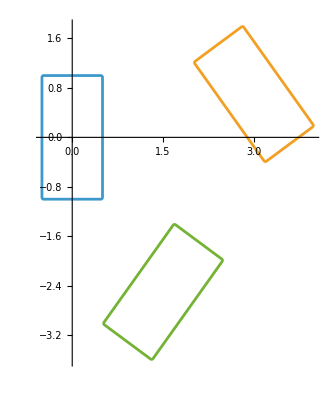

```mathematica
rectangles=ListLinePlot[{house1,house2Shift,house3Shift},AspectRatio->Automatic]
```

```mathematica
(*****************Сохраняем точки VP*********************)
```

```mathematica
leftX=-0.6;
rightX=4.2;
downY=-4.2;
upY=2.0;
```

```mathematica
(rightX-leftX)/10
```

0.48

```mathematica
(upY-downY)/10
```

0.62

```mathematica
nX=48;(*количество точек по горизонтали nX+1*)
nY=62;(*количество точек по вертикали nY+1*)
```

```mathematica
VP=Flatten[N[Table[N[{leftX+i(rightX-leftX)/nX,downY+j(upY-downY)/nY}],{j,0,nY},{i,0,nX}],16],1];
```

```mathematica
{xMin1,xMax1}=MinMax[geom1[[All,1]]] ;
{yMin1,yMax1}=MinMax[geom1[[All,2]]] ;
```

```mathematica
rotatedRectangle2=Polygon[house2Shift];
rotatedRectangle3=Polygon[house3Shift];
```

```mathematica
VPnew=DeleteCases[VP,_?(RegionMember[rotatedRectangle2,#]||RegionDistance[rotatedRectangle2,#]<0.05&)];
```

```mathematica
VPnew2=DeleteCases[VPnew,{x_,y_}/;xMin1<=x<=xMax1&&yMin1<=y<=yMax1];
```

```mathematica
VPnew3=DeleteCases[VPnew2,_?(RegionMember[rotatedRectangle3,#]||RegionDistance[rotatedRectangle3,#]<0.05&)];
```

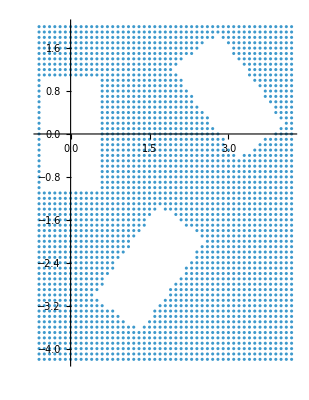

```mathematica
points=ListPlot[VPnew3,AspectRatio->Automatic]
```

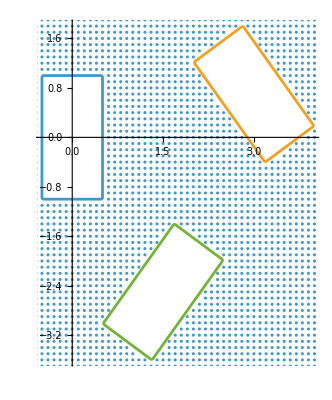

```mathematica
Show[rectangles,points]
```

```mathematica
VPnew3
```

```mathematica
Export["pointsVP",
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.12   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2024/01/14     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2024 I. Marchevsky, K. Sokol, E. Ryatina, A. Kolganova   |
*-----------------------------------------------------------------------------*
| File name: pointsVP"<>StringRepeat[" ",57]<>"|
| Info: Points for velocity and pressure computation "<>"(n="<>ToString[Length[VPnew3]]<>")"<>StringRepeat[" ",23-StringLength["n="<>ToString[Length[VPnew3]]]]<>"|
\*---------------------------------------------------------------------------*/"
}
~Join~{"n = "<>ToString[Length[VPnew3]]<>";"}~Join~{"points = {"}~Join~((ToString[SetPrecision[#,17]]<>",")&/@(VPnew3[[1;;-2]]))~Join~((ToString[SetPrecision[#,17]])&/@(VPnew3[[{-1}]]))~Join~{" };"},"Table"]
```

pointsVP

```mathematica
Import["pointsVP","Table"][[13;;]]
```